```mathematica
GH1[s_]:=(0.06782 s^6+0.01532 s^5+0.00887 s^4+0.001185 s^3+ 5.072*10^(-5) s^2+5.276*10^(-7) s-2.884*10^(-23))/(s^7+0.2738 s^6+0.1572 s^5+0.004018 s^4+9.088*10^(-5) s^3)
```

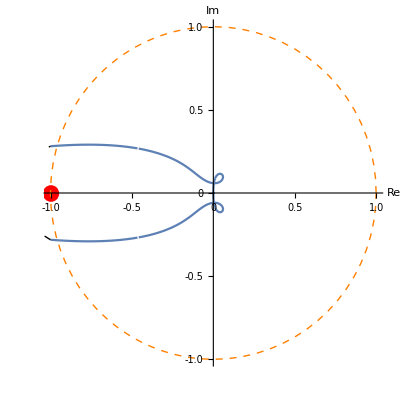

```mathematica
nyMFLR = Show[NyquistPlot[TransferFunctionModel[GH1[s],s],PlotRange->{-1,1}],Graphics[{Red, Disk[{-1,0},0.05], Orange, Dashed, Circle[{0,0},1]}], AxesLabel->{Re, Im}]
```

```mathematica
GH[s_]:= (10^(-3)*(2.218s^4+ .2024s^3+ .2528s^2+ .003805s))/(s^6+ 0.273796s^5+ .157203s^4+ .00401842s^3 +.000090883s^2)
```

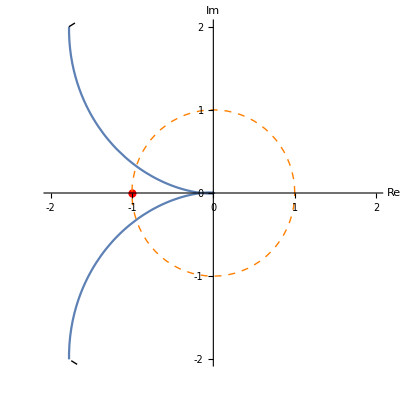

```mathematica
pltNy =Show[NyquistPlot[TransferFunctionModel[GH[s],s],PlotRange->{-2,2}],Graphics[{Red, Disk[{-1,0},0.05], Orange, Dashed, Circle[{0,0},1]}], AxesLabel->{Re, Im}]
```

```mathematica
Export["NyGHMA.jpg",pltNy,ImageResolution->1000]
```

NyGHMA.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["NyGH.jpg"]]]
```

```mathematica
Export["NyGH.jpg",nyMFLR,ImageResolution->1000]
```

NyGH.jpg